0.24180405166868976056562803766339908791511710570222

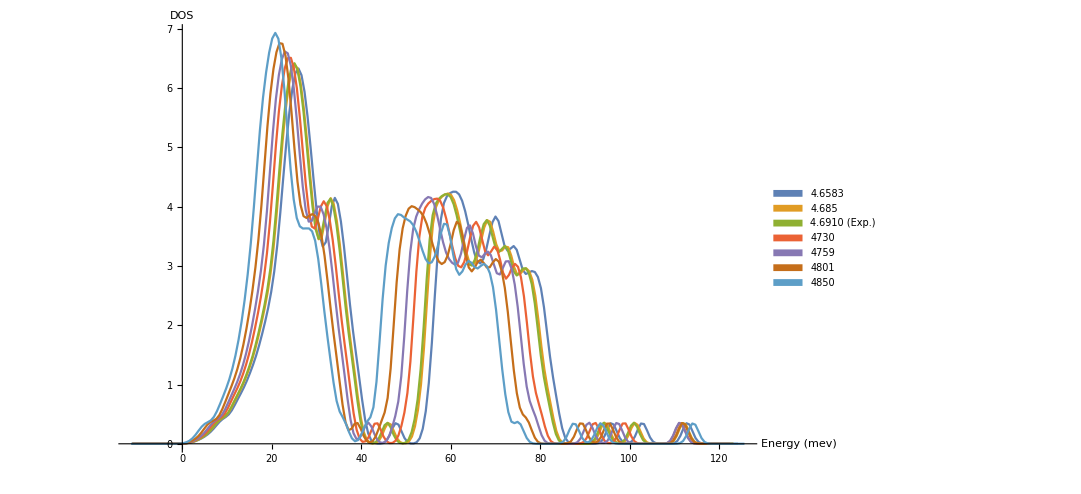

```mathematica
meVtoTHz=(1/4.13558)

labeldos={"4575","4.625","4.6583","4.685","4.6910 (Exp.)","4730","4759","4801","4850"};
labeldos1={"4.6583","4.685","4.6910 (Exp.)","4730","4759","4801","4850"};
kjmol2evatom=1/(96.487*64);
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Defect_annealed/DOS"];
file={"DOS_all"};
dosAll=ReadList[file[[1]],{Number, Number}];
dosmeV=Transpose@{Transpose[dosAll][[1]]/meVtoTHz,Transpose[dosAll][[2]]*meVtoTHz};

ListPlot[Table[Partition[dosmeV,201][[i]],{i,3,9}],PlotLegends->SwatchLegend[labeldos1],Joined->True,AxesLabel->{"Energy (mev)","DOS"},ImageSize->800]
DOSfits=Table[Interpolation[Partition[dosmeV,201][[i]]],{i,3,9}];
```

```mathematica
(*Plan

Extract the energy of the middle mode for band 1 and band 2 using technique in 4575
Use peaks=FindPeaks[values] to extract molecule states
Make a list of comega, zomega and m1omega m2omega and m3omega

Make harmonic heat capcity function with DOS preactor 3*1/192(96*Zr+_part + 93*C_part + 1*C_mol1 + 1*C_mol2 + 1*C_mol3)

Make a list of Einstein oscillator frequencies from atomic displacement and calculate same

Import perfect and defective DOS


*)
```

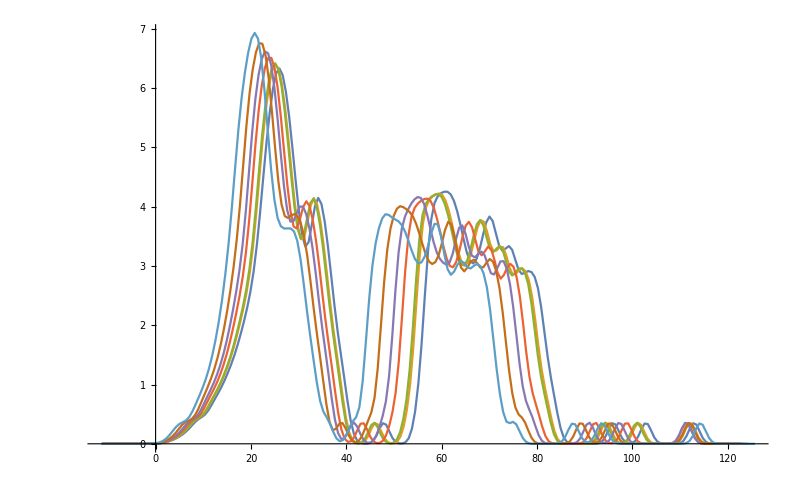

```mathematica
dos=Table[Partition[dosmeV,201][[i]],{i,3,9}];
ListLinePlot[dos,ImageSize->800]
```

-Graphics-

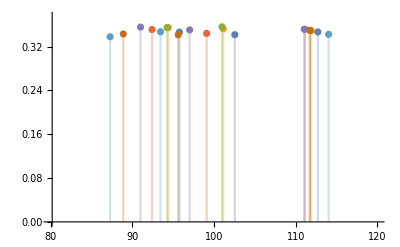

```mathematica
peaks=Table[PeakDetect[Transpose[dos[[i]]][[2]]],{i,1,7}];
molfreq=Table[DeleteCases[Take[(dos peaks)[[i]],-65],{0.,0.}],{i,1,7}];
molfreq//TableForm;
horizontalListPlotFill[listplot_,axisOrigin_: 0]:=listplot/.Point[a__]:>{Point[a],Opacity[0.3],Line[{{#1,axisOrigin},{#1,#2}}&@@@a]};
horizontalListPlotFill[ListPlot[fmolall]]
horizontalListPlotFill@ListPlot[Evaluate@molfreq,PlotRange->{{80,120},{0,0.375}}]
```

```mathematica
(*Heat capcity function*)
(*Make harmonic heat capcity function with DOS preactor 3*1/192(96*Zr+_part + 93*C_part + 1*C_mol1 + 1*C_mol2 + 1*C_mol3)*)
```

```mathematica
harmCv[T_,freqs_,dosfactor_,freqfactor_]:=dosfactor*(K2meV*((((freqfactor*freqs))/(K2meV*T))^2)*Exp[((freqfactor*freqs))/(K2meV*T)]/((Exp[((freqfactor*freqs))/(K2meV*T)]-1)^2))
```

```mathematica
deltas={a_,b_}->{a};
fmolall=molfreq/.deltas//Flatten;
fmol1=Transpose[Partition[fmolall,3]][[1]];
fmol2=Transpose[Partition[fmolall,3]][[2]];
fmol3=Transpose[Partition[fmolall,3]][[3]];
```

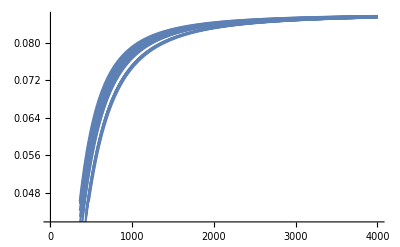

```mathematica
(*Defect heat capacity*)
Show@Table[Plot[Partition[harmCv[T,fmolall,1,1],3][[i]],{T,1,4000}],{i,1,7}]
```

-49658.+42646.4 x-13718.2 x^2+1961.36 x^3-105.241 x^4

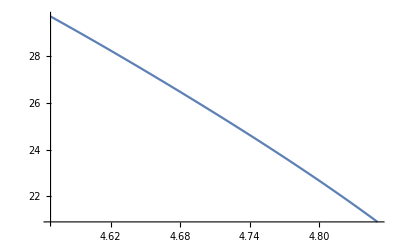

{27.1305,26.3295,26.1474,24.9432,24.0211,22.6334,20.9082}

526242.-443216. x+140051. x^2-19673. x^3+1036.41 x^4

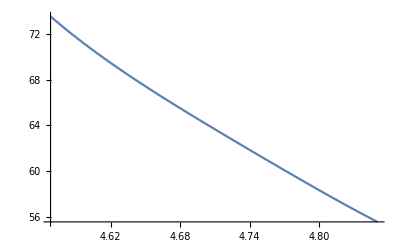

{66.8759,65.188,64.8169,62.4499,60.7228,58.271,55.5724}

```mathematica
(*Perfect DOS Einstein Frequencies taken from DOS book - DOS_analysis_at_six_volumes*)
vols={4.6583,4.685,4.6910,4.730,4.759,4.801,4.850};
perfvols={4.685,4.730,4.759,4.801,4.850};
perfZrfreqs={26.329538754361874,24.943209151536333,24.021100225884023,22.63344907985203,20.908163645232506};
perfCfreqs={65.1879672429008,62.449863381584365,60.722769401686904,58.27102760314375,55.572432293540885};

(*Zr Einstein freqs*)
fitzr=Fit[Transpose@{perfvols,perfZrfreqs},{1,x,x*x,x*x*x,x*x*x*x},x]
Plot[fitzr,{x,4.5683,4.850}]
fzall=fitzr/.x->vols

(*C Einstein freqs*)
fitc=Fit[Transpose@{perfvols,perfCfreqs},{1,x,x*x,x*x*x,x*x*x*x},x]
Plot[fitc,{x,4.5683,4.850}]
fcall=fitc/.x->vols
```

```mathematica
fcall
```

{66.8759,65.188,64.8169,62.4499,60.7228,58.271,55.5724}

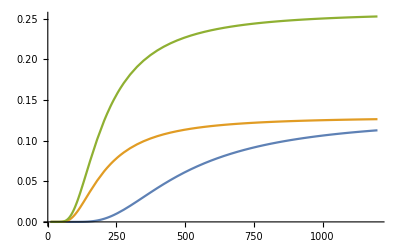

```mathematica
(*Perfect harmonic*)
Plot[{harmCv[T,fcall,3/2,2][[1]],harmCv[T,fzall,3/2,2][[1]],harmCv[T,fzall,3/2,2][[1]]+harmCv[T,fzall,3/2,2][[1]]},{T,10,1200}]
```

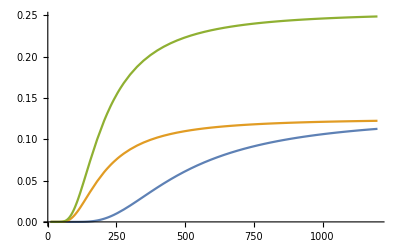

```mathematica
(*Perfect harmonic scaled for defect*)
Plot[{harmCv[T,fcall,3*96/192,2][[1]],harmCv[T,fzall,3*(96-3)/192,2][[1]],harmCv[T,fzall,3*96/192,2][[1]]+harmCv[T,fzall,3*(96-3)/192,2][[1]]},{T,10,1200}]
```

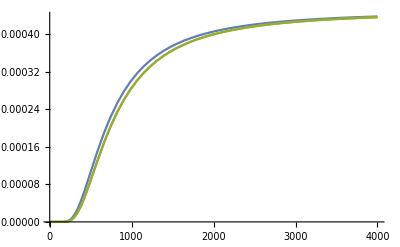

```mathematica
(*Defect molecule*)
Plot[{harmCv[T,fmol1,1/192,2][[1]],harmCv[T,fmol2,1/192,2][[1]],harmCv[T,fmol2,1/192,2][[1]]},{T,10,4000}]
```

```mathematica
(*Defect molecule*)
molcv=Table[harmCv[T,fmol1,3/192,2][[i]]+harmCv[T,fmol2,3/192,2][[i]]+harmCv[T,fmol2,3/192,2][[i]],{i,1,7}];
partialcv=Table[harmCv[T,fzall,3*96/192,2][[i]]+harmCv[T,fzall,3*(96-3)/192,2][[i]],{i,1,7}];
perfectcv=Table[harmCv[T,fzall,3*96/192,2][[i]]+harmCv[T,fzall,3*(96)/192,2][[i]],{i,1,7}];
```

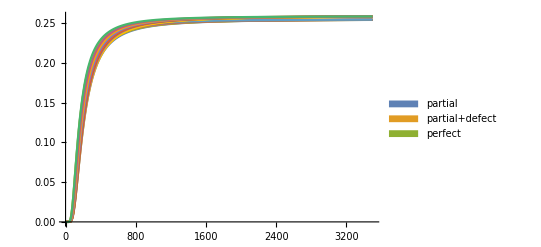

```mathematica
Plot[{partialcv,molcv+partialcv,perfectcv},{T,0,3500},PlotLegends->SwatchLegend[{"partial","partial+defect","perfect"}],PlotRange->All]
```

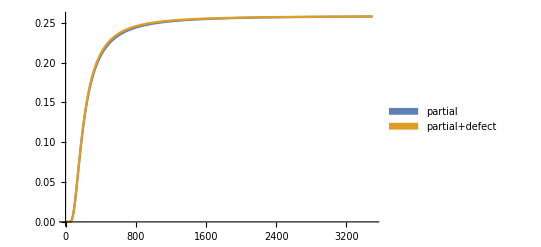

```mathematica
Plot[{molcv[[1]]+partialcv[[1]],perfectcv[[1]]},{T,1,3500},PlotLegends->SwatchLegend[{"partial","partial+defect","perfect"}],PlotRange->All]
```

```mathematica
(*Now compare to pure qha perfect and defect*)
64*3
```

```mathematica
(*Make harmonic heat capcity function with DOS preactor 3*1/192(96*Zr+_part + 93*C_part + 1*C_mol1 + 1*C_mol2 + 1*C_mol3)*)

SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/ZrC_QHA_output"];
qhaNormal={"QHA_normal/e-v.dat","QHA_normal/volume_expansion.dat","QHA_normal/volume-temperature.dat","QHA_normal/gruneisen-temperature.dat","QHA_normal/gibbs-temperature.dat","QHA_normal/bulk_modulus-temperature.dat","QHA_normal/Cp-temperature.dat","QHA_normal/dsdv-temperature.dat"};
Cv4685={"T_heat_4685_normal","T_heatcap_4685_defect"}
qhaperfectvolexp=Table[ReadList[qhaNormal[[i]],{Number, Number}],{i,2,2}];
qhaperfectvolt=Table[ReadList[qhaNormal[[i]],{Number, Number}],{i,3,3}];
qhaperfectcp=Table[ReadList[qhaNormal[[i]],{Number, Number}],{i,7,7}];
qhaperfectdsdv=Table[ReadList[qhaNormal[[i]],{Number, Number}],{i,8,8}];

qhaDefect={"QHA_defect/e-v.dat","QHA_defect/volume_expansion.dat","QHA_defect/volume-temperature.dat","QHA_defect/gruneisen-temperature.dat","QHA_defect/gibbs-temperature.dat","QHA_defect/bulk_modulus-temperature.dat","QHA_defect/Cp-temperature.dat","QHA_defect/dsdv-temperature.dat"};
qhadefectvolexp=Table[ReadList[qhaDefect[[i]],{Number, Number}],{i,2,2}];
qhadefectvolt=Table[ReadList[qhaDefect[[i]],{Number, Number}],{i,3,3}];
qhadefectcp=Table[ReadList[qhaDefect[[i]],{Number, Number}],{i,7,7}];
qhadefectsdv=Table[ReadList[qhaNormal[[i]],{Number, Number}],{i,8,8}];
```

{T_heat_4685_normal,T_heatcap_4685_defect}

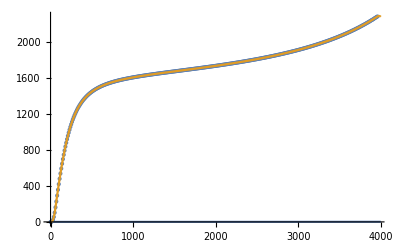

```mathematica
Show[ListPlot[qhadefectcp],Plot[{x*Interpolation[qhadefectsdv[[1]]][x]*Interpolation[qhadefectvolexp[[1]]][x],Interpolation[qhadefectcp[[1]]][x]},{x,1,4000}]]
```

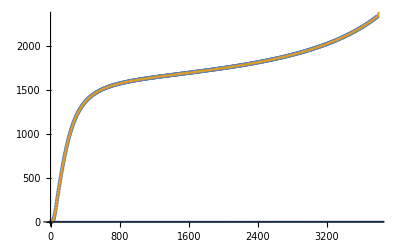

```mathematica
Show[ListPlot[qhaperfectcp],Plot[{x*Interpolation[qhaperfectdsdv[[1]]][x]*Interpolation[qhaperfectvolexp[[1]]][x],Interpolation[qhaperfectcp[[1]]][x]},{x,1,4000}]]
```

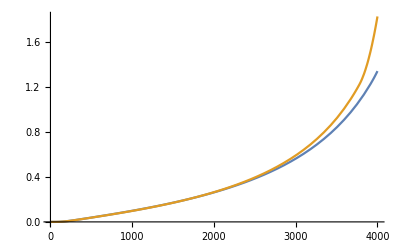

```mathematica
Plot[{x*Interpolation[qhadefectsdv[[1]]][x]*Interpolation[qhadefectvolt[[1]]]'[x],x*Interpolation[qhaperfectdsdv[[1]]][x]*Interpolation[qhaperfectvolt[[1]]]'[x]},{x,1,4000}]
```

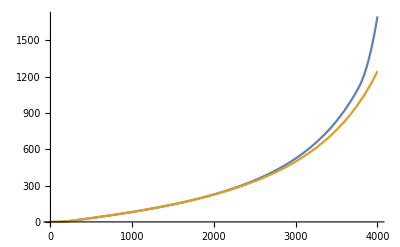

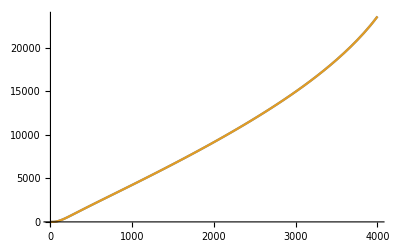

```mathematica
Plot[{x*Interpolation[qhaperfectdsdv[[1]]][x]*Interpolation[qhaperfectvolt[[1]]]'[x]*Interpolation[qhadefectvolt[[1]]][x],x*Interpolation[qhadefectsdv[[1]]][x]*Interpolation[qhadefectvolt[[1]]]'[x]*Interpolation[qhadefectvolt[[1]]][x]},{x,1,4000}]
(*All of the difference between Cp defect and Cp harmonic comes from one term Cp = Cv + T *dSdV*dVdT - *)
Plot[{x*Interpolation[qhaperfectdsdv[[1]]][x]*Interpolation[qhadefectvolt[[1]]][x],x*Interpolation[qhadefectsdv[[1]]][x]*Interpolation[qhadefectvolt[[1]]][x]},{x,1,4000}]
```

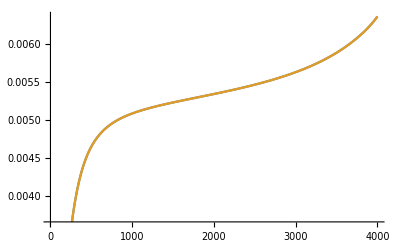

```mathematica
Plot[{Interpolation[qhaperfectdsdv[[1]]][x],Interpolation[qhadefectsdv[[1]]][x]},{x,1,4000}]
```

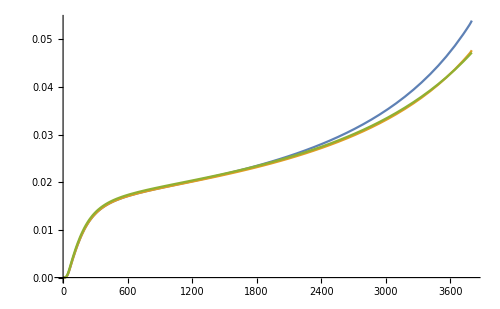

```mathematica
Plot[{Interpolation[qhaperfectvolt[[1]]]'[x],Interpolation[qhaperfectvolt[[1]]]'[x]*(1-x*x*x/7800^3),Interpolation[qhadefectvolt[[1]]]'[x]},{x,1,3800},ImageSize->500]
```

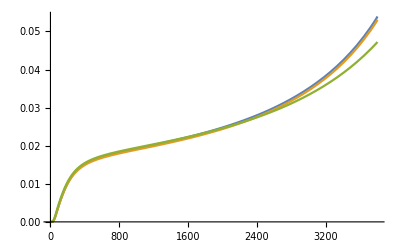

```mathematica
(*If we assume the defect mode doesn't take part*)Plot[{Interpolation[qhaperfectvolt[[1]]]'[x],Interpolation[qhaperfectvolt[[1]]]'[x]*(1-1/64),Interpolation[qhadefectvolt[[1]]]'[x]},{x,1,3800}]
```

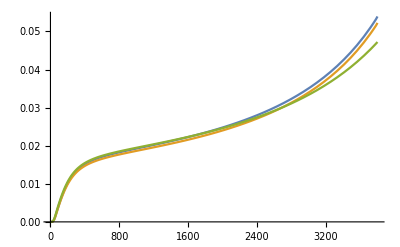

```mathematica
(*IUf we assume the defect mode doesn't take part*)Plot[{Interpolation[qhaperfectvolt[[1]]]'[x],Interpolation[qhaperfectvolt[[1]]]'[x]*(1-2/64),Interpolation[qhadefectvolt[[1]]]'[x]},{x,1,3800}]
```

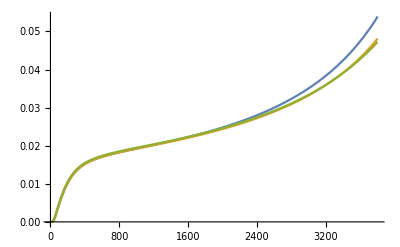

```mathematica
Plot[{Interpolation[qhaperfectvolt[[1]]]'[x],Interpolation[qhaperfectvolt[[1]]]'[x]*(1-(x/8000)^3),Interpolation[qhadefectvolt[[1]]]'[x]},{x,1,3800}]
```

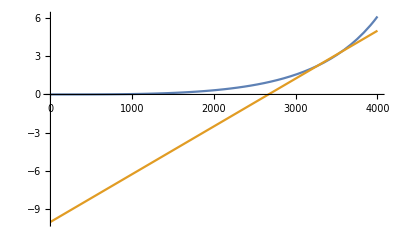

```mathematica
Plot[{Interpolation[qhadefectvolt[[1]]][x]*Interpolation[qhadefectvolt[[1]]]'[x]*(x/8000)^3,15x/4000-10},{x,1,4000}]
```

```mathematica
Plot[{Interpolation[qhaperfectvolt[[1]]]'[x],Interpolation[qhaperfectvolt[[1]]]'[x]*(1-1/64)-Interpolation[qhaperfectvolt[[1]]]'[x]*(1/64),Interpolation[qhadefectvolt[[1]]]'[x]},{x,1,3800}]
```

-Graphics-

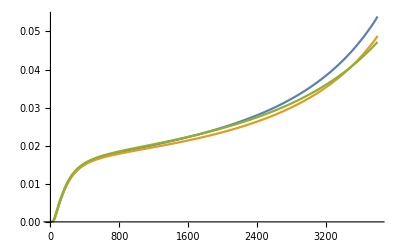

```mathematica
Plot[{Interpolation[qhaperfectvolt[[1]]]'[x],Interpolation[qhaperfectvolt[[1]]]'[x]*(1-x/40000),Interpolation[qhadefectvolt[[1]]]'[x]},{x,1,3800}]
```

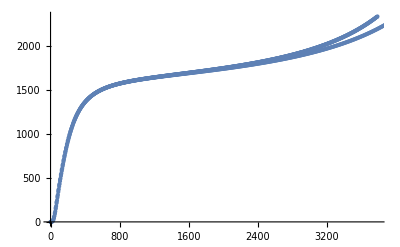

```mathematica
Show[ListPlot[qhaperfectcp],ListPlot[qhadefectcp]]
```

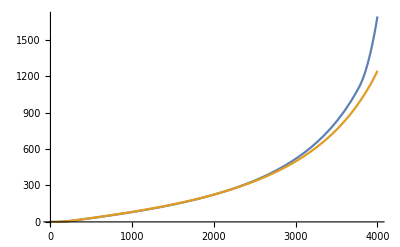

```mathematica
Plot[{x*Interpolation[qhaperfectdsdv[[1]]][x]*Interpolation[qhaperfectvolt[[1]]]'[x]*Interpolation[qhaperfectvolt[[1]]][x],x*Interpolation[qhadefectsdv[[1]]][x]*Interpolation[qhadefectvolt[[1]]]'[x]*Interpolation[qhadefectvolt[[1]]][x]},{x,1,4000}]
```

```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/ZrC_QHA_output"];
Cv4685={"T_heat_4685_normal","T_heatcap_4685_defect","T_heatcap_4850normal","T_heatcap_4850_defect"};
Cv=Table[ReadList[Cv4685[[i]],{Number, Number}],{i,1,4}];
```

```mathematica
Cv4685perfectqha=Interpolation[Cv[[1]]];
Cv4685defectqha=Interpolation[Cv[[2]]];
```

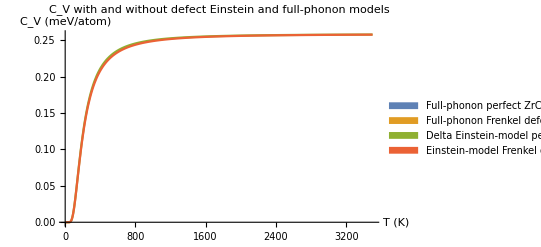

```mathematica
(*Comparison of Cv for Einstein and full phonon models*)
(*Cv is barely affected by change in the defect and Einstein model describes Cv very well.*)
Plot[{(kjmol2evatom)Cv4685perfectqha[x],(kjmol2evatom)Cv4685defectqha[x],perfectcv[[1]],molcv[[1]]+partialcv[[1]]},{T,1,3500},PlotLegends->SwatchLegend[{"Full-phonon perfect ZrC","Full-phonon Frenkel defective","Delta Einstein-model perfect ZrC","Einstein-model Frenkel defective"}],PlotRange->All,PlotLabel->"C_V with and without defect\nEinstein and full-phonon models",AxesLabel->{"T (K)","C_V (meV/atom)"}]
```

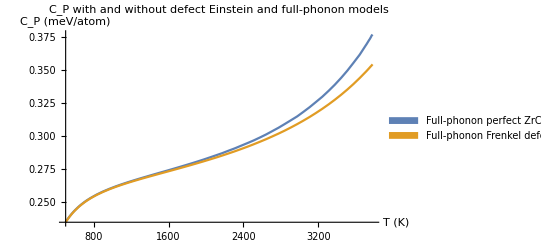

```mathematica
(*However the ZrC Cp is dependent on the defect*)
Plot[{(kjmol2evatom)Interpolation[qhaperfectcp[[1]]][x],(kjmol2evatom)Interpolation[qhadefectcp[[1]]][x]},{x,500,3780},PlotLegends->SwatchLegend[{"Full-phonon perfect ZrC","Full-phonon Frenkel defective"}],PlotLabel->"C_P with and without defect\nEinstein and full-phonon models",AxesLabel->{"T (K)","C_P (meV/atom)"}]
```

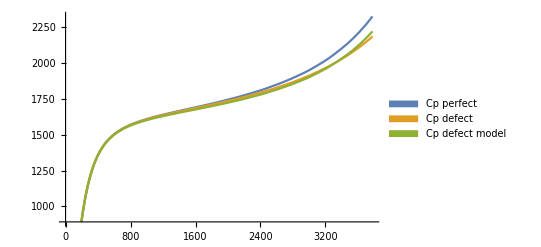

```mathematica
(*Can we approximate the Ein*)
Plot[{Interpolation[qhaperfectcp[[1]]][x],Interpolation[qhadefectcp[[1]]][x],Interpolation[qhaperfectcp[[1]]][x]-(3/32)x*Interpolation[qhaperfectdsdv[[1]]][x]*Interpolation[qhaperfectvolt[[1]]]'[x]*Interpolation[qhaperfectvolt[[1]]][x]},{x,1,3780},PlotLegends->SwatchLegend[{"Cp perfect","Cp defect","Cp defect model"}]]
```